# Superposition of several discrete waves (periodic pulse)

## Play

```mathematica
Clear["Global`*"]
```

```mathematica
f[t_]=Sum[(4 Sin[2 π ν t])/(ν π),{ν,100,900,200}]
```

Sin[200 π t]/(25 π)+Sin[600 π t]/(75 π)+Sin[1000 π t]/(125 π)+Sin[1400 π t]/(175 π)+Sin[1800 π t]/(225 π)

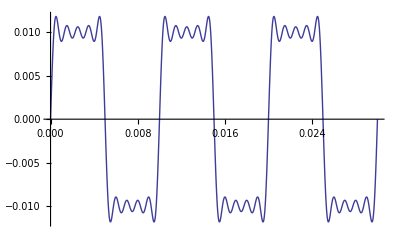

```mathematica
Plot[f[t],{t,0,0.03}]
```

```mathematica
play=Play[f[t],{t,0,10}]
```

-Graphics-

## Export

### Get current notebook directory

```mathematica
CurrentNotebookDirectory=NotebookDirectory[SelectedNotebook[]]
```

/Users/Soha/Google Drive/Café Planck/2-Physics/03-Sound waves/

### Set Directory to current notebook directory

```mathematica
SetDirectory[CurrentNotebookDirectory]
```

/Users/Soha/Google Drive/Café Planck/2-Physics/03-Sound waves

### Get current notebook name

```mathematica
CurrentNotebookName=StringTake[ToString[SelectedNotebook[]],{18,StringPosition[ToString[SelectedNotebook[]],">",1][[1,1]]-1}]
```

Superposition of several discrete waves (periodic pulse).nb

### Export

```mathematica
fileName=StringJoin[StringDrop[CurrentNotebookName,-3],".wav"];
```

```mathematica
Export[fileName,play];
```